Supplemental notebook to R. Herrmann, “Combining arbitrary order global Padé approximation of the Mittag-Leffler function with its addition formula for a significant accuracy boost”, arXiv:2408.10257 [physics.gen-ph]. 	 	
https://doi.org/10.48550/arXiv.2408.10257
R. Herrmann, 
Fractional Calculus - Introduction for Physicists, 
4th edition, World Scientific Publishing, Singapore. 
Chapter 2
https://www.worldscientific.com/worldscibooks/10.1142/14345#t=aboutBook

# Combining arbitrary order global Padé approximation of the Mittag-Leffler function with its addition formula for a significant accuracy boost

Richard Herrmann

gigaHedron, r.herrmann@fractionalcalculus.org

October 2024.

## Introduction

The combination of the global Padé approximation of the Mittag-Leffler function with its addition formula for the case α < 1 yields significantly higher accuracy results for a given arbitrary order n. We present a solution in terms of a Mathematica notebook to determine the general structure of the system of linear equations to be solved.

## Program pade2.nb

### start clean

```mathematica
Clear[alp,bet,vars]
```

### order of PadeApproximant

```mathematica
n=2
```

2

### asymptotics

```mathematica
a[x_]:=+Gamma[bet-alp] x*Sum[(-x)^k/Gamma[bet+alp k],{k,0,n+1}];
b[x_]:=-Gamma[bet-alp] x*Sum[(-x)^(-k)/Gamma[bet-alp k],{k,1,n}];
```

### collect parameters

```mathematica
ps=Symbol["p"<>ToString[#]]&/@Range[0,n-1];
qs=Symbol["q"<>ToString[#]]&/@Range[0,n-1];
vars = Append[ps,qs] // Flatten

xs=(x^#)&/@Range[0,n-1];
```

{p0,p1,q0,q1}

### Pade polynomials p/q

```mathematica
p=Total[ps xs]+x^n;      
q=Total[qs xs]+x^n;
```

### collect conditions

```mathematica
ca=CoefficientList[p-q a[x],x];
cb=CoefficientList[p/x^n-q/x^n b[x],1/x];
```

### collect equations

```mathematica
condsa=(ca[[#]]==0)&/@Range[n+1]
condsb=(cb[[#]]==0)&/@Range[2,n]
conds=Append[condsa,condsb]//Flatten
```

{p0==0,p1-(q0 Gamma[-alp+bet])/Gamma[bet]==0,1-(q1 Gamma[-alp+bet])/Gamma[bet]+(q0 Gamma[-alp+bet])/Gamma[alp+bet]==0}

{p1-q1+Gamma[-alp+bet]/Gamma[-2 alp+bet]==0}

{p0==0,p1-(q0 Gamma[-alp+bet])/Gamma[bet]==0,1-(q1 Gamma[-alp+bet])/Gamma[bet]+(q0 Gamma[-alp+bet])/Gamma[alp+bet]==0,p1-q1+Gamma[-alp+bet]/Gamma[-2 alp+bet]==0}

### set up matrix for linear algebra package solver m.x + b

```mathematica
vector = Append[ca[[#]] & /@ Range[n+1],cb[[#]] & /@ Range[2,n]] // Flatten;
coefficientsMatrix=Coefficient[#,vars]&/@vector ;
bs = coefficientsMatrix.vars - vector;
coefficientsMatrix /= Gamma[bet-alp];
bs /= Gamma[bet-alp];
```

### show traditional form

```mathematica
coefficientsMatrix // MatrixForm //TraditionalForm  
bs  //TraditionalForm
coefficientsMatrix // MatrixForm   
bs  //TraditionalForm
```

(1/(bet-alp) | 0 | 0 | 0
0 | 1/(bet-alp) | -1/bet | 0
0 | 0 | 1/(alp+bet) | -1/bet
0 | 1/(bet-alp) | 0 | -1/(bet-alp))

{0,0,-1/(bet-alp),-1/(bet-2 alp)}

(1/Gamma[-alp+bet] | 0 | 0 | 0
0 | 1/Gamma[-alp+bet] | -1/Gamma[bet] | 0
0 | 0 | 1/Gamma[alp+bet] | -1/Gamma[bet]
0 | 1/Gamma[-alp+bet] | 0 | -1/Gamma[-alp+bet])

{0,0,-1/(bet-alp),-1/(bet-2 alp)}

### solve with LinearSolve

```mathematica
solution = FullSimplify[LinearSolve[coefficientsMatrix,bs]]
```

{0,((-Gamma[bet] Gamma[-2 alp+bet]+Gamma[-alp+bet]^2) Gamma[alp+bet])/(Gamma[-2 alp+bet] (Gamma[bet]^2-Gamma[-alp+bet] Gamma[alp+bet])),(Gamma[bet] (Gamma[bet] Gamma[-2 alp+bet]-Gamma[-alp+bet]^2) Gamma[alp+bet])/(Gamma[-2 alp+bet] Gamma[-alp+bet] (-Gamma[bet]^2+Gamma[-alp+bet] Gamma[alp+bet])),(Gamma[bet] (Gamma[bet] Gamma[-alp+bet]-Gamma[-2 alp+bet] Gamma[alp+bet]))/(Gamma[-2 alp+bet] (Gamma[bet]^2-Gamma[-alp+bet] Gamma[alp+bet]))}

### solve with Solve

```mathematica
padeApproximant = Solve[conds,vars]
padeApproximant=  FullSimplify[p/q/x/Gamma[bet-alp] /. padeApproximant  ];
```

{{p0→0,p1→-((Gamma[bet] Gamma[-2 alp+bet]-Gamma[-alp+bet]^2) Gamma[alp+bet])/(Gamma[-2 alp+bet] (Gamma[bet]^2-Gamma[-alp+bet] Gamma[alp+bet])),q0→(Gamma[bet] (Gamma[bet] Gamma[-2 alp+bet]-Gamma[-alp+bet]^2) Gamma[alp+bet])/(Gamma[-2 alp+bet] Gamma[-alp+bet] (-Gamma[bet]^2+Gamma[-alp+bet] Gamma[alp+bet])),q1→(Gamma[bet]^2 Gamma[-alp+bet]-Gamma[bet] Gamma[-2 alp+bet] Gamma[alp+bet])/(Gamma[-2 alp+bet] (Gamma[bet]^2-Gamma[-alp+bet] Gamma[alp+bet]))}}

### unit test

0.5

1.501

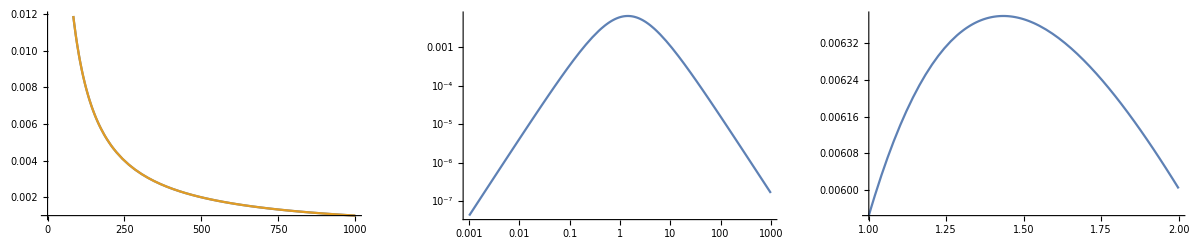

```mathematica
alp = 0.5
bet = 1.501
ug = 10^-3;
og = 10^3;
fig1=Plot[{padeApproximant,MittagLefflerE[alp,bet,-x]},{x,ug,og}];
fig2=LogLogPlot[1-padeApproximant/MittagLefflerE[alp,bet,-x],{x,ug,og}];
fig3=Plot[1-padeApproximant/MittagLefflerE[alp,bet,-x],{x,1,2}];
GraphicsRow[{fig1,fig2, fig3}, ImageSize->Full]
```